# Gas expansion simulation

## Solenoid valve exit

## figure a: snap shot

```mathematica
(* -- import -- *)
raw=Import[NotebookDirectory[]<>"raw/dim2.mx"];

(* -- options and labels -- *)
colorFunc=If[NumberQ[#],ColorData["TemperatureMap"][#/600],Black]&;

tlb={FontSize->14,FontColor->Black,Text[Framed["t = 50 ms",Background->White,FrameStyle->{Black,AbsoluteThickness[1]},ImageSize->{80,25},Alignment->Center],{-325,0},{-1,-1}]};
plb={FontSize->14,FontColor->Black,Text[Framed[ToString[#]<>" bar",Background->White,FrameStyle->{Black,AbsoluteThickness[1]},ImageSize->{70,25},Alignment->Center],{69.5,-9.7},{1,-1}]}&;

vlb={
{Pink,AbsoluteThickness[5],Line[{{0,-3},{0,3}}]},
{Pink,AbsoluteThickness[2],Arrowheads[{0,.02}],Arrow[{{0,-6.5},{0,-3.5}}]},
{FontSize->14,FontColor->Pink,Text["valve exit",{0,-6.5},{0,1}]}
};
avgZone={EdgeForm[{Red,AbsoluteThickness[2],AbsoluteDashing[6]}],FaceForm[Transparent],Rectangle[{0,-3},{70,3}]};
ticks={Black,AbsoluteThickness[.5],Line[Append[Table[{{i,-10},{i,10}},{i,-10,70,10}],{{-12,0},{70,0}}]]};

{xMin,xMax,yMin,yMax}={-12.,70.,-10.,10.};

optClr={
PlotRange->{{0,300},{0,10}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain,FontColor->Black},

Frame->True,
FrameTicks->{{None,None},{Table[{i,Null,{.015,0}},{i,0,300,100}],Table[{i,i,{.015,0}},{i,0,300,100}]}},
FrameLabel->{{"Temperature (K)",None},{None,None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],
RotateLabel->False,

GridLines->None,
ImageSize->(130*2)*(72/25.4),AspectRatio->.06,
ImagePadding->{{400,15},{5,30}}
};

optPlt={
PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain,FontColor->Black},

Frame->True,
FrameTicks->{{Table[{i,i,{0,0}},{i,-10,10,5}],None},{Table[{i,i,{0,0}},{i,-10,70,10}],None}},
FrameLabel->{{"r (mm)",None},{"z (mm)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

ImageSize->(130*2)*(72/25.4),
ImagePadding->{{50,15},{45,15}}

};

(* -- colorbar -- *)
barLegend=Graphics[
Raster[{List@@@Map[colorFunc,Range[0,300,1]]},{{0,0},{300,10}}],
Epilog->{
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
tlb
},
optClr
];

(* -- plot -- *)
plt=Show[
Graphics@Raster[raw,{{xMin,yMin},{xMax,yMax}},ColorFunction->colorFunc,ColorFunctionScaling->True],
Epilog->{ticks,vlb,avgZone,plb[1]},
optPlt
];

(* -- merge -- *)
gfa=Column[{barLegend,plt}];

Print[gfa];
```

## figure b: average temperature compared w/ exp.

```mathematica
(* -- import -- *)
expT=Import[NotebookDirectory[]<>"raw/expT.mx"];
avgT=Import[NotebookDirectory[]<>"raw/avgT.mx"];

(* -- plot -- *)
gfb=ListLinePlot[

{expT,avgT},

Epilog->{
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
{Pink,AbsoluteThickness[3],Line[{{0,150},{0,300}}]},
{Pink,AbsoluteThickness[2],Arrowheads[{-.02,0}],Arrow[{{1,275},{4,275}}]},
Text[Style["valve exit",{FontColor->Pink,FontSize->14,FontWeight->Plain}],{5,275},{-1,0}]
},

Joined->{False,True},
ScalingFunctions->"Linear",

PlotRange->{{0,70},{150,300}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{
{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]},
{Black,Opacity[1],AbsoluteDashing[6],AbsoluteThickness[2]}
},

PlotMarkers->{
{Graphics[{
EdgeForm[{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]}],
FaceForm[{RGBColor[.54,.62,.72,1]}],
Disk[]},PlotRangePadding->0],Offset[10]},
None
},

IntervalMarkers->"Bands",
IntervalMarkersStyle->Directive[
EdgeForm[{Opacity[1],AbsoluteThickness[1]}],FaceForm[RGBColor[.54,.62,.72,.5]]
],

PlotLegends->Placed[
LineLegend[
{{},Directive[Black,AbsoluteDashing[6],AbsoluteThickness[2]]},
{"experiment","COMSOL simulation"},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMarkers->{
Graphics[{
EdgeForm[{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]}],
FaceForm[{RGBColor[.54,.62,.72,1]}],
Disk[]}],
None
},
LegendMarkerSize->{{30,10}},
LegendMargins->1,LegendLayout->"Column"],
{Scaled@{.95,.1},{1,0}}],

Frame->True,
FrameTicks->{Table[{{i,i,{.015,0}},{i,Null,{.015,0}}},{i,150,300,50}]ᵀ,Table[{{i,i,{.015,0}},{i,Null,{.015,0}}},{i,0,70,10}]ᵀ},
FrameLabel->{{"Average temperature (K)",None},{"z (mm)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{50,15},{45,20}},
AspectRatio->.3,
ImageSize->(130*2)*(72/25.4)

];

Print[gfb];
```

## merge figures

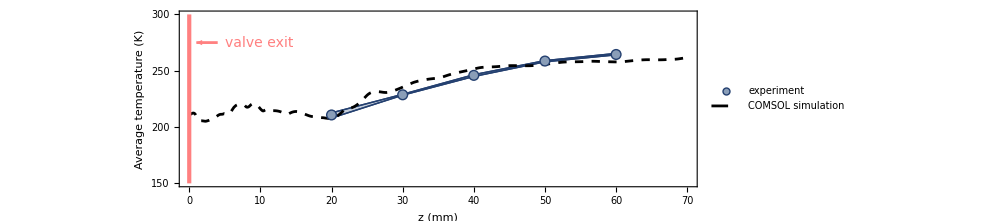
-Graphics-
-Graphics-

```mathematica
gf=Grid[{{gfa},{gfb}}];
Print[gf];
Export[NotebookDirectory[]<>"comsolSolenoid.pdf",gf];
```

## Compressor exit

## figure a: snap shot

```mathematica
(* -- import -- *)
raw=Import[NotebookDirectory[]<>"raw/dim1.mx"];

(* -- options and labels -- *)
colorFunc=If[NumberQ[#],ColorData["TemperatureMap"][#/600],Black]&;

tlb={FontSize->14,FontColor->Black,Text[Framed["t = 300 μs",Background->White,FrameStyle->{Black,AbsoluteThickness[1]},ImageSize->{80,25},Alignment->Center],{-325,0},{-1,-1}]};
plb={FontSize->14,FontColor->Black,Text[Framed[ToString[#]<>" bar",Background->White,FrameStyle->{Black,AbsoluteThickness[1]},ImageSize->{70,25},Alignment->Center],{59.7,0},{1,0}]}&;
ticks={Black,AbsoluteThickness[.5],Line[Append[Table[{{i,-2},{i,2}},{i,0,40,20}],{{-3,0},{60,0}}]]};

{xMin,xMax,yMin,yMax}={-3.,60.,-2.,2.};

optClr={
PlotRange->{{0,300},{0,10}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain,FontColor->Black},

Frame->True,
FrameTicks->{{None,None},{Table[{i,Null,{.015,0}},{i,0,300,100}],Table[{i,i,{.015,0}},{i,0,300,100}]}},
FrameLabel->{{"Temperature (K)",None},{None,None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],
RotateLabel->False,

GridLines->None,
ImageSize->(130*2)*(72/25.4),AspectRatio->.06,
ImagePadding->{{400,15},{5,30}}
};

optPlt={
PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain,FontColor->Black},

Frame->True,
FrameTicks->None,
FrameLabel->None,
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

ImageSize->(130*2)*(72/25.4),
ImagePadding->{{50,15},{0,10}},
AspectRatio->.05
};

(* -- colorbar -- *)
barLegend=Graphics[
Raster[{List@@@Map[colorFunc,Range[0,300,1]]},{{0,0},{300,10}}],
Epilog->{
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
tlb
},
optClr
];

(* -- plot -- *)
pltFunc[p_]:=Show[
Graphics@Raster[raw[p],{{xMin,yMin},{xMax,yMax}},ColorFunction->colorFunc,ColorFunctionScaling->True],
Epilog->{ticks,plb[p]},
optPlt
];

(* -- merge -- *)
gfa=Column[{

barLegend,
pltFunc[10],
pltFunc[50],
pltFunc[100],
Show[
pltFunc[200],
FrameTicks->{{Table[{i,i,{0,0}},{i,{-2,2}}],None},{Table[{i,i,{0,0}},{i,{-3,0,20,40,60}}],None}},
FrameLabel->{{"r (mm)",None},{"z (mm)",None}},
ImagePadding->{{50,15},{45,10}}
]

}];

Print[gfa];
```

## figure b: minimum temperature

```mathematica
(* -- import -- *)
minT=Import[NotebookDirectory[]<>"raw/minT.mx"];

(* -- plot -- *)
gfb=ListLinePlot[

minT,

Epilog->{
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

Joined->True,
ScalingFunctions->"Linear",

PlotRange->{{0,220},{0,300}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]}},

PlotMarkers->{
{Graphics[{
EdgeForm[{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]}],
FaceForm[{RGBColor[.54,.62,.72,1]}],
Disk[]},PlotRangePadding->0],Offset[10]},
None
},

IntervalMarkers->"Bands",
IntervalMarkersStyle->Directive[
EdgeForm[{Opacity[1],AbsoluteThickness[1]}],FaceForm[RGBColor[.54,.62,.72,.5]]
],

PlotLegends->Placed[
LineLegend[
{Directive[RGBColor[.14,.25,.44,1],AbsoluteThickness[1]]},
{"COMSOL simulation"},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMarkers->{
Graphics[{
EdgeForm[{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]}],
FaceForm[{RGBColor[.54,.62,.72,1]}],
Disk[]}]
},
LegendMarkerSize->{{30,10}},
LegendMargins->1,LegendLayout->"Row"],
{Scaled@{.95,.1},{1,0}}],

Frame->True,
FrameTicks->{
Table[{{i,i,{.015,0}},{i,Null,{.015,0}}},{i,0,300,100}]ᵀ,{Table[{i,If[Mod[i,50]==0,i,Null],{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}],
Table[{i,Null,{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}]}
},
FrameLabel->{{"Minimum temperature (K)",None},{"Pipe pressure (bar)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{50,15},{45,20}},
AspectRatio->.3,
ImageSize->(130*2)*(72/25.4)

];

Print[gfb];
```

## merge figures

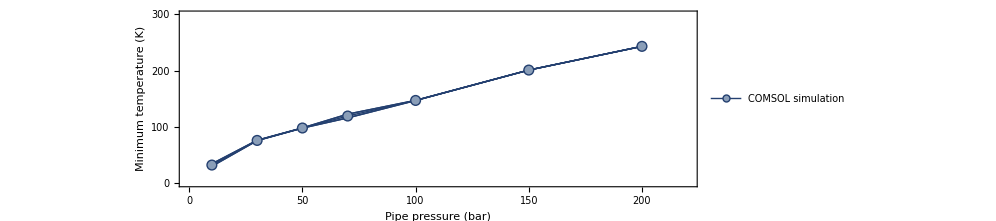
-Graphics-
-Graphics-

```mathematica
gf=Grid[{{gfa},{gfb}}];
Print[gf];
Export[NotebookDirectory[]<>"comsolCompressor.pdf",gf];
```